```mathematica
Plot3D[Total[({{1,2},{1,3}}.{x1,x2}-{0,0})^2],{x1,-10,10},{x2,-10,10}]
```

-Graphics3D-

```mathematica
Total[({{a11,a12},{a21,a22}}.{x1,x2}-{b1,b2})^2]
```

(-b1+a11 x1+a12 x2)^2+(-b2+a21 x1+a22 x2)^2

```mathematica
D[Total[({{a11,a12},{a21,a22}}.{x1,x2}-{b1,b2})^2],x1]
```

2 a11 (-b1+a11 x1+a12 x2)+2 a21 (-b2+a21 x1+a22 x2)

```mathematica
x={x1,x2,x3,x4};
i14=Transpose[{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}];
i58=Transpose[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0},{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}];
i9={0,0,0,0,0,0,0,0,1,0};
i10={0,0,0,0,0,0,0,0,0,1};
```

```mathematica
F[x_]:=Total[(1/(1+E^(-(1/(1+E^(-((1/(1+E^(-(x)))).i14.w)))i9.w+1/(1+E^(-((1/(1+E^(-(x)))).i58.w)))i10.w)))-y)^2]
```

```mathematica
(1/(1+E^(-(x)))).i58.w
```

w5/(1+ⅇ^-x1)+w6/(1+ⅇ^-x2)+w7/(1+ⅇ^-x3)+w8/(1+ⅇ^-x4)

```mathematica
D[F[x],w1]//Simplify
```

(ⅇ^((ⅇ^x1 w1)/(1+ⅇ^x1)+w10/(1+ⅇ^(-(ⅇ^x1 w5)/(1+ⅇ^x1)-(ⅇ^x2 w6)/(1+ⅇ^x2)-(ⅇ^x3 w7)/(1+ⅇ^x3)-(ⅇ^x4 w8)/(1+ⅇ^x4)))+(ⅇ^x2 w2)/(1+ⅇ^x2)+(ⅇ^x3 w3)/(1+ⅇ^x3)+(ⅇ^x4 w4)/(1+ⅇ^x4)+w9/(1+ⅇ^(-(ⅇ^x1 w1)/(1+ⅇ^x1)-(ⅇ^x2 w2)/(1+ⅇ^x2)-(ⅇ^x3 w3)/(1+ⅇ^x3)-(ⅇ^x4 w4)/(1+ⅇ^x4)))+x1) w9)/((1+ⅇ^((ⅇ^x1 w1)/(1+ⅇ^x1)+(ⅇ^x2 w2)/(1+ⅇ^x2)+(ⅇ^x3 w3)/(1+ⅇ^x3)+(ⅇ^x4 w4)/(1+ⅇ^x4)))^2 (1+ⅇ^(w10/(1+ⅇ^(-(ⅇ^x1 w5)/(1+ⅇ^x1)-(ⅇ^x2 w6)/(1+ⅇ^x2)-(ⅇ^x3 w7)/(1+ⅇ^x3)-(ⅇ^x4 w8)/(1+ⅇ^x4)))+w9/(1+ⅇ^(-(ⅇ^x1 w1)/(1+ⅇ^x1)-(ⅇ^x2 w2)/(1+ⅇ^x2)-(ⅇ^x3 w3)/(1+ⅇ^x3)-(ⅇ^x4 w4)/(1+ⅇ^x4)))))^2 (1+ⅇ^x1))

```mathematica
D[(1/(1+E^(-(1/(1+E^(-((1/(1+E^(-(x)))).i14.w)))i9.w+1/(1+E^(-((1/(1+E^(-(x)))).i58.w)))i10.w)))-y),w1]//Simplify
```

(ⅇ^((ⅇ^x1 w1)/(1+ⅇ^x1)+w10/(1+ⅇ^(-(ⅇ^x1 w5)/(1+ⅇ^x1)-(ⅇ^x2 w6)/(1+ⅇ^x2)-(ⅇ^x3 w7)/(1+ⅇ^x3)-(ⅇ^x4 w8)/(1+ⅇ^x4)))+(ⅇ^x2 w2)/(1+ⅇ^x2)+(ⅇ^x3 w3)/(1+ⅇ^x3)+(ⅇ^x4 w4)/(1+ⅇ^x4)+w9/(1+ⅇ^(-(ⅇ^x1 w1)/(1+ⅇ^x1)-(ⅇ^x2 w2)/(1+ⅇ^x2)-(ⅇ^x3 w3)/(1+ⅇ^x3)-(ⅇ^x4 w4)/(1+ⅇ^x4)))+x1) w9)/((1+ⅇ^((ⅇ^x1 w1)/(1+ⅇ^x1)+(ⅇ^x2 w2)/(1+ⅇ^x2)+(ⅇ^x3 w3)/(1+ⅇ^x3)+(ⅇ^x4 w4)/(1+ⅇ^x4)))^2 (1+ⅇ^(w10/(1+ⅇ^(-(ⅇ^x1 w5)/(1+ⅇ^x1)-(ⅇ^x2 w6)/(1+ⅇ^x2)-(ⅇ^x3 w7)/(1+ⅇ^x3)-(ⅇ^x4 w8)/(1+ⅇ^x4)))+w9/(1+ⅇ^(-(ⅇ^x1 w1)/(1+ⅇ^x1)-(ⅇ^x2 w2)/(1+ⅇ^x2)-(ⅇ^x3 w3)/(1+ⅇ^x3)-(ⅇ^x4 w4)/(1+ⅇ^x4)))))^2 (1+ⅇ^x1))

```mathematica
(1/(1+E^(-(1/(1+E^(-((1/(1+E^(-(x)))).i14.w)))i9.w+1/(1+E^(-((1/(1+E^(-(x)))).i58.w)))i10.w)))-y)
```

1/(1+ⅇ^(-w10/(1+ⅇ^(-w5/(1+ⅇ^-x1)-w6/(1+ⅇ^-x2)-w7/(1+ⅇ^-x3)-w8/(1+ⅇ^-x4)))-w9/(1+ⅇ^(-w1/(1+ⅇ^-x1)-w2/(1+ⅇ^-x2)-w3/(1+ⅇ^-x3)-w4/(1+ⅇ^-x4)))))-y

```mathematica
F[x]
```

2+1/(1+ⅇ^(-w10/(1+ⅇ^(-w5/(1+ⅇ^-x1)-w6/(1+ⅇ^-x2)-w7/(1+ⅇ^-x3)-w8/(1+ⅇ^-x4)))-w9/(1+ⅇ^(-w1/(1+ⅇ^-x1)-w2/(1+ⅇ^-x2)-w3/(1+ⅇ^-x3)-w4/(1+ⅇ^-x4)))))-y

```mathematica
Manipulate[Plot[(1/(1+ⅇ^(-w10/(1+ⅇ^(-w5/(1+ⅇ^-x1)-w6/(1+ⅇ^-x2)-w7/(1+ⅇ^-x3)-w8/(1+ⅇ^-x4)))-w9/(1+ⅇ^(-w1/(1+ⅇ^-x1)-w2/(1+ⅇ^-x2)-w3/(1+ⅇ^-x3)-w4/(1+ⅇ^-x4)))))-y)^2,{w10,-1,1}],{x1,-1,1},{x2,-1,1},{x3,-1,1},{x4,-1,1},{w1,-1,1},{w2,-1,1},{w3,-1,1},{w4,-1,1},{w5,-1,1},{w6,-1,1},{w7,-1,1},{w8,-1,1},{w9,-1,1},{y,{0,1}}]
```

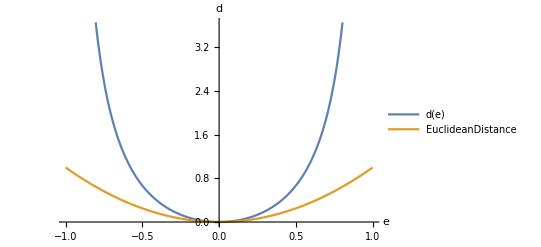

```mathematica
Plot[{(1/(1-e)+1/(1+e))-2,e^2},{e,-1,1},AxesLabel->{e,d},PlotLegends->{"d(e)","EuclideanDistance"}]
```

```mathematica
*
```

```mathematica
D[-2/(-1+e^2),e]
```

(4 e)/((-1+e^2)^2)

```mathematica
Simplify[1/(1-e)+1/(1+e)-2]
```

-(2 e^2)/(-1+e^2)

```mathematica
{{0, 0, 1}, {0, 1, 1}, {1, 1, 1}}
```

```mathematica
Needs["ErrorBarPlots`"]
```

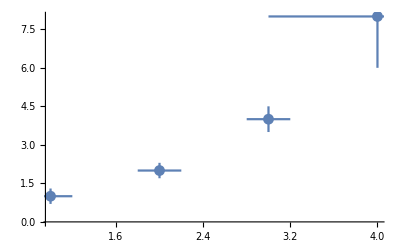

```mathematica
ErrorListPlot[{{{1,1},ErrorBar[0.2,0.3]},{{2,2},ErrorBar[0.2,0.3]},{{3,4},ErrorBar[0.2,0.5]},{{4,8},ErrorBar[1,2]}},
ErrorBarFunction->Automatic]
```

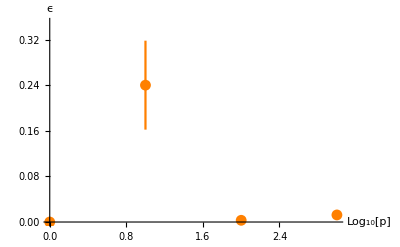

```mathematica
ErrorListPlot[
{
{{0,0},ErrorBar[0]},
{{1,.24},ErrorBar[0.078]},
{{2,.0030},ErrorBar[0.0024]},
{{3,0.0124},ErrorBar[0.0044]}
},PlotRange->{0,.35},AxesLabel->{"Log_10[p]","ϵ"},PlotStyle->Orange]
```

```mathematica
StandardDeviation[{0.0220,
0.0100,
0.0110,
0.0100,
0.0100,
0.0100,
0.0100,
0.0110,
0.0180}]
```

0.00441902

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[],"ds2"}]]
```

/Users/poincare/Dropbox/Documentos/DMKM/01 Lyon/Courseware/Op/Lab/Lab001/ds2

```mathematica
x=Import["x100.xls"];
x=x[[1]];
y=Import["y100.csv"];
y=Flatten[y];
xh=Import["xh.mat"];
xh=xh[[1]];
yh=Import["yh.xls"];
yh=Flatten[yh];
yt=Import["y1000.xls"];
yt=Flatten[yt];
```

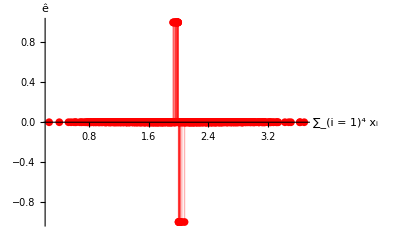

```mathematica
ListPlot[
{Table[{Part[Total/@xh,i],yh[[i]]-yt[[i]]},{i,1,Length[yt]}]},PlotRange->All,PlotMarkers->{"•", 8},Filling->Axis,AxesLabel->{"∑_(i = 1)^4 x_i","ê"},PlotStyle->Red]
```

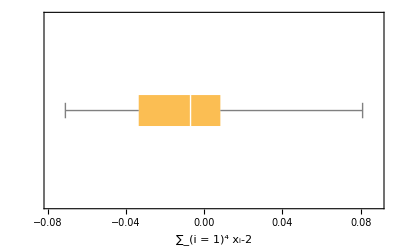

```mathematica
BoxWhiskerChart[Select[Table[{Part[Total/@xh,i],yh[[i]]-yt[[i]]},{i,1,Length[yt]}],#[[2]]≠0&][[All,1]]-2,BarOrigin->Left,FrameLabel->{"∑_(i = 1)^4 x_i-2"}]
```

```mathematica
Select[Table[{Part[Total/@xh,i],yh[[i]]-yt[[i]]},{i,1,Length[yt]}],#[[2]]≠0&][[All,1]]-2
```

{0.007,0.,-0.023,-0.021,-0.045,-0.007,-0.004,0.014,-0.071,0.003,-0.033,0.015,0.012,-0.04,0.007,-0.062,-0.027,-0.047,0.045,-0.035,0.081,0.024,-0.013,-0.006,-0.013,-0.009,-0.068,-0.006,0.023}

```mathematica
Mean[Select[Table[{Part[Total/@xh,i],yh[[i]]-yt[[i]]},{i,1,Length[yt]}],#[[2]]≠0&][[All,1]]-2]
```

-0.0103103

```mathematica
w={-0.75,-0.940,-.986,-.892,4803.786,4565.815,4122.838,4515.028,-16840.135,1662.110};
```

```mathematica
Clear[x]
xt=x1+x2+x3+x4
```

x1+x2+x3+x4

```mathematica
(1)/(1+E^(-(1/(1+E^(-((1/(1+E^(-(x)))).i14.w)))i9.w+1/(1+E^(-((1/(1+E^(-(x)))).i58.w)))i10.w)))
```

1/(1+ⅇ^(-1662.11/(1+ⅇ^(0.-4803.79/(1+ⅇ^-x1)-4565.82/(1+ⅇ^-x2)-4122.84/(1+ⅇ^-x3)-4515.03/(1+ⅇ^-x4)))+16840.1/(1+ⅇ^(0.+0.75/(1+ⅇ^-x1)+0.94/(1+ⅇ^-x2)+0.986/(1+ⅇ^-x3)+0.892/(1+ⅇ^-x4)))))

```mathematica
Manipulate[Evaluate[(1)/(1+E^(-(1/(1+E^(-((1/(1+E^(-(x)))).i14.w)))i9.w+1/(1+E^(-((1/(1+E^(-(x)))).i58.w)))i10.w)))],{x1,-1,1},{x2,-1,1},{x3,-1,1},{x4,-1,1}]
```